## Brain Data

### 1. Data Input

```mathematica
graph1 = Import["D:\\bme\\8\\Önlab\\valós hálózatok\\Brain\\Hagman Data\\HBadjmatricesScale1.wdx"];
(*graph2 = Import["D:\\bme\\8\\Önlab\\valós hálózatok\\Brain\\Hagman Data\\HBadjmatricesScale2.wdx"];
graph3 = Import["D:\\bme\\8\\Önlab\\valós hálózatok\\Brain\\Hagman Data\\HBadjmatricesScale3.wdx"];
graph4 = Import["D:\\bme\\8\\Önlab\\valós hálózatok\\Brain\\Hagman Data\\HBadjmatricesScale4.wdx"]*);
graph5 = Import["D:\\bme\\8\\Önlab\\valós hálózatok\\Brain\\Hagman Data\\HBadjmatricesScale5.wdx"];

graph11 = graph1[[1]];
(*graph21 = graph2[[1]];
graph31 = graph3[[1]];
graph41 = graph4[[1]];*)
graph51 = graph5[[1]];
```

### 2. Visualize Data

#### Graph1_1

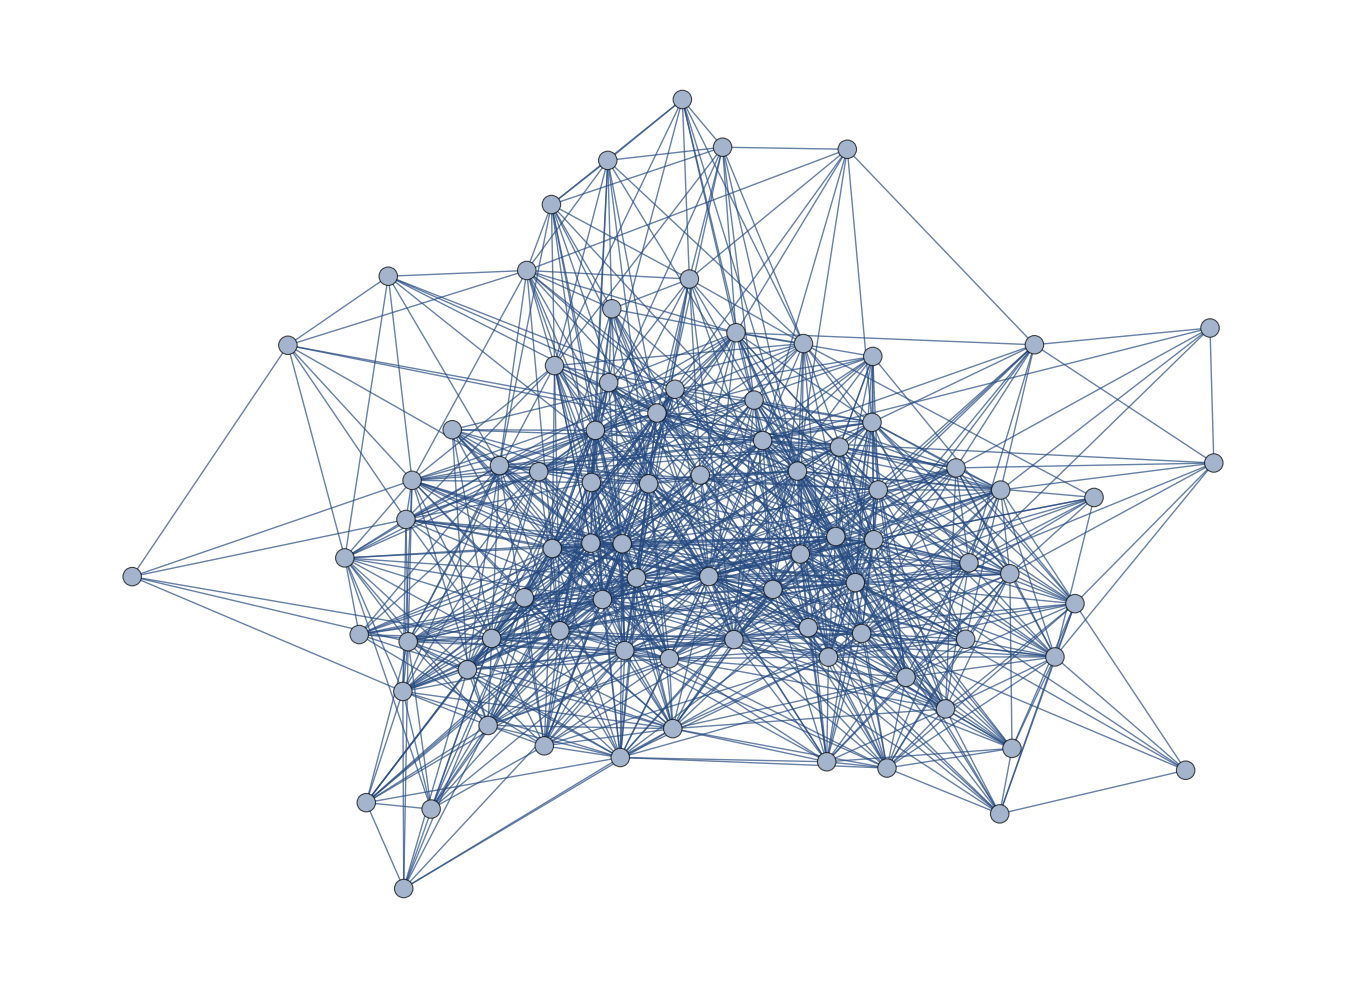

```mathematica
AdjacencyGraph[graph11]
```

```mathematica
vertices = 83;
```

```mathematica
vertexdegree ={26,18,10,21,25,23,36,43,21,37,17,10,12,17,9,25,13,41,34,28,16,22,31,28,25,14,6,9,27,23,16,21,6,23,36,33,45,41,24,36,24,37,13,14,35,20,27,33,35,30,36,16,12,14,16,18,29,13,44,24,39,24,23,38,30,19,9,9,6,27,25,10,24,12,33,35,31,43,36,23,25,20,55};
```

```mathematica
dist = vertexdegree/vertices
```

{26/83,18/83,10/83,21/83,25/83,23/83,36/83,43/83,21/83,37/83,17/83,10/83,12/83,17/83,9/83,25/83,13/83,41/83,34/83,28/83,16/83,22/83,31/83,28/83,25/83,14/83,6/83,9/83,27/83,23/83,16/83,21/83,6/83,23/83,36/83,33/83,45/83,41/83,24/83,36/83,24/83,37/83,13/83,14/83,35/83,20/83,27/83,33/83,35/83,30/83,36/83,16/83,12/83,14/83,16/83,18/83,29/83,13/83,44/83,24/83,39/83,24/83,23/83,38/83,30/83,19/83,9/83,9/83,6/83,27/83,25/83,10/83,24/83,12/83,33/83,35/83,31/83,43/83,36/83,23/83,25/83,20/83,55/83}

```mathematica
sortedDist = ReverseSort[dist]
```

{55/83,45/83,44/83,43/83,43/83,41/83,41/83,39/83,38/83,37/83,37/83,36/83,36/83,36/83,36/83,36/83,35/83,35/83,35/83,34/83,33/83,33/83,33/83,31/83,31/83,30/83,30/83,29/83,28/83,28/83,27/83,27/83,27/83,26/83,25/83,25/83,25/83,25/83,25/83,24/83,24/83,24/83,24/83,24/83,23/83,23/83,23/83,23/83,23/83,22/83,21/83,21/83,21/83,20/83,20/83,19/83,18/83,18/83,17/83,17/83,16/83,16/83,16/83,16/83,14/83,14/83,14/83,13/83,13/83,13/83,12/83,12/83,12/83,10/83,10/83,10/83,9/83,9/83,9/83,9/83,6/83,6/83,6/83}

#### Degree distribution

```mathematica
ListLinePlot[sortedDist,PlotTheme->"Scientific",Filling->Automatic,Mesh->All]
```

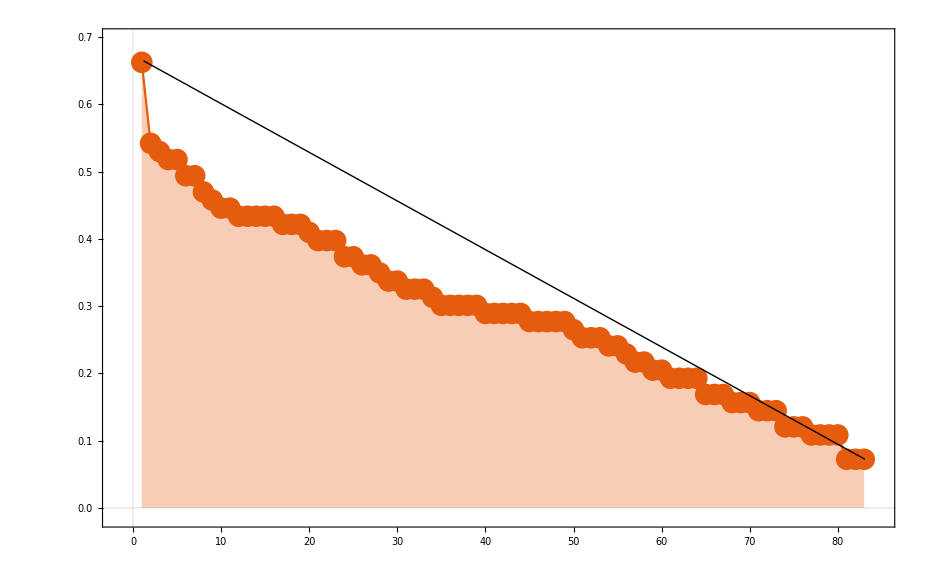

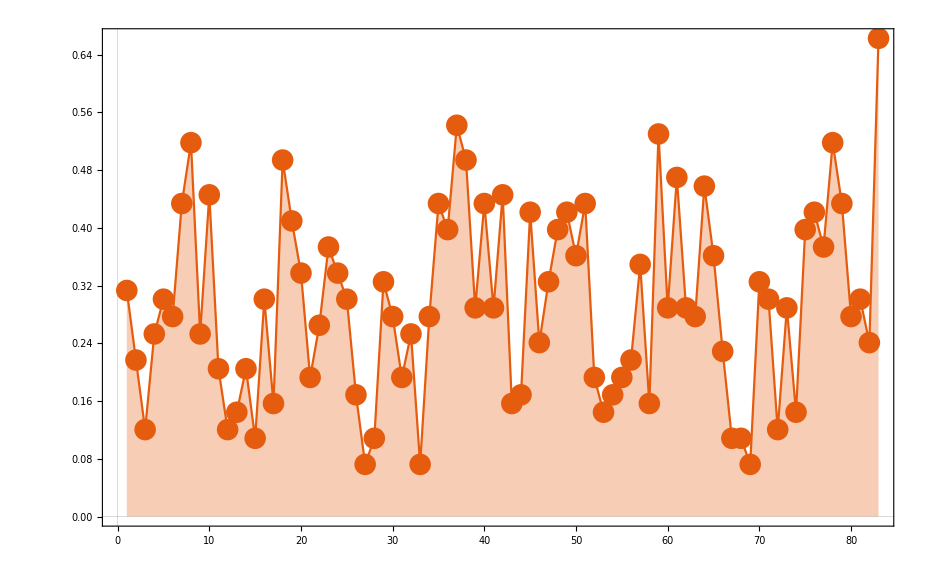

```mathematica
ListLinePlot[dist,Filling->Automatic,PlotTheme->"Scientific",Mesh->All]
```

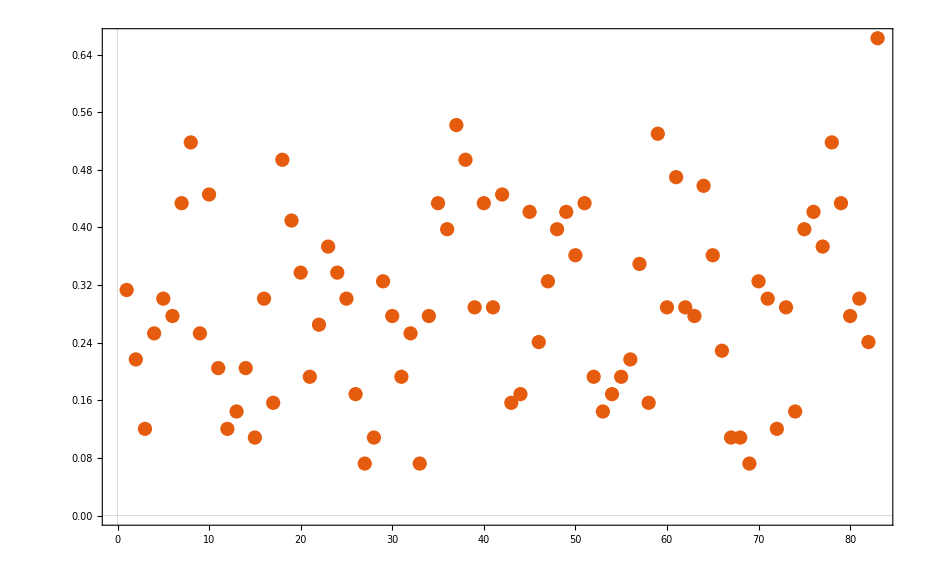

```mathematica
ListPlot[dist,PlotTheme->"Scientific"]
```

```mathematica
total_vertexdegree = Total[vertexdegree]*1/2
```

Set::write: Tag List in total:Blank[{26,18,10,21,25,23,36,43,21,37,17,10,12,17,9,25,13,41,34,28,16,22,31,28,25,14,6,9,27,23,16,21,6,23,36,33,45,41,24,36,24,37,13,14,35,20,27,33,35,30,«33»}] is Protected.

1017

#### Graph2_1

#### Graph3_1

#### Graph4_1

#### Graph5_1

```mathematica
AdjacencyGraph[graph51]
```

```mathematica
vertices5 = 1015
```

1015

```mathematica
vertexdegree5 = {7,45,51,42,22,8,6,15,2,9,3,29,16,15,13,26,40,50,22,16,26,11,12,25,8,17,27,27,20,7,6,4,9,8,26,36,20,43,19,17,17,39,35,64,34,39,24,65,21,15,12,42,60,62,30,26,10,44,38,17,29,44,41,5,33,51,15,27,15,10,52,55,15,20,21,49,44,33,54,42,42,47,40,24,18,18,46,34,29,48,30,25,56,64,70,39,33,33,42,36,31,41,45,16,40,37,35,42,27,40,18,24,9,42,32,19,23,23,32,24,34,34,51,36,59,13,13,12,42,69,39,15,14,13,22,18,14,31,21,18,21,15,27,12,22,45,38,30,13,24,50,28,25,9,18,19,36,50,46,40,24,44,47,37,22,34,30,24,13,31,42,30,19,16,37,42,33,31,30,17,14,18,0,42,6,19,24,44,34,16,43,27,43,56,43,32,27,14,29,21,14,19,29,13,25,30,14,11,7,28,20,24,17,3,21,16,7,5,18,6,5,17,27,9,5,6,18,17,23,6,8,27,15,34,27,26,19,16,13,27,39,10,17,9,7,17,30,20,14,11,9,15,32,38,20,42,51,23,27,23,41,31,43,35,33,19,21,45,47,20,27,35,41,12,28,17,3,11,31,70,78,73,7,10,41,31,32,7,9,20,28,51,58,19,24,44,40,58,16,5,19,21,12,20,58,39,29,65,70,30,22,54,41,20,43,53,42,12,16,39,25,41,29,41,40,43,35,21,28,22,22,28,4,5,21,26,5,14,37,25,39,15,7,14,23,14,43,39,74,50,56,39,23,22,11,40,22,51,27,21,28,24,22,27,10,26,18,18,14,23,15,11,32,26,19,34,18,5,13,20,15,16,10,4,32,11,5,13,31,24,6,10,35,33,21,37,49,25,51,16,30,20,13,4,3,8,16,15,12,9,6,7,4,2,14,4,24,0,26,28,1,7,18,11,14,14,51,5,21,76,40,57,43,70,52,80,20,17,9,11,25,27,20,24,25,16,29,23,10,1,4,33,16,23,26,18,32,38,11,11,10,22,23,29,27,14,40,24,24,15,17,22,42,14,16,13,44,13,22,7,29,7,10,15,11,10,25,17,7,17,45,21,13,17,14,27,29,52,19,25,6,171,114,254,160,48,143,58,34,13,39,25,55,54,9,49,45,10,10,3,44,6,63,30,24,13,32,14,19,18,29,20,61,34,10,49,6,35,9,9,22,29,37,12,26,20,39,5,22,74,24,31,30,25,29,25,10,27,11,29,25,39,21,34,29,36,19,18,53,29,36,58,34,29,13,10,30,45,54,24,18,23,42,27,31,35,28,23,31,48,26,27,17,25,30,57,35,45,72,71,34,38,38,12,41,27,32,22,35,24,36,23,28,32,40,35,42,32,22,43,26,31,32,38,44,34,43,30,50,75,41,8,13,20,60,61,37,50,63,48,31,25,29,33,23,28,9,21,44,26,12,21,26,16,26,39,22,38,47,34,54,44,37,17,24,39,35,12,60,39,46,86,40,34,12,22,31,19,19,27,45,14,15,19,14,28,32,32,21,27,30,20,20,28,31,34,34,41,14,45,68,14,31,23,24,57,31,25,19,19,25,56,30,31,27,11,14,8,12,35,15,12,10,17,10,12,26,26,31,13,15,9,19,15,12,11,15,36,20,24,38,5,20,20,12,13,16,14,17,26,21,13,14,14,17,7,30,12,11,25,41,10,15,26,13,26,25,28,32,18,32,35,29,53,50,51,34,35,41,11,31,46,34,23,7,28,35,35,38,40,32,46,74,62,53,16,64,73,50,47,13,41,43,33,12,52,18,12,17,23,13,28,18,11,14,11,20,44,25,27,25,44,49,34,21,41,19,44,32,25,56,54,58,37,21,30,42,33,57,35,6,5,50,21,40,30,40,47,20,37,5,37,33,71,48,48,43,26,24,34,60,43,38,27,22,20,57,8,13,28,26,25,22,45,43,54,29,31,26,19,26,28,9,24,12,13,9,12,22,2,24,40,24,14,49,22,16,8,45,14,9,8,58,14,16,21,15,9,5,10,12,16,12,9,9,14,19,7,9,8,5,8,0,0,42,0,5,14,8,18,32,53,36,40,42,59,70,93,28,10,26,43,40,38,34,33,59,13,27,78,20,17,7,57,26,26,34,34,24,18,29,13,35,22,17,19,15,28,30,23,59,18,29,28,16,48,58,10,24,35,102,5,20,35,6,9,10,21,40,6,30,17,31,43,10,19,25,14,67,59,43,25,11,11,8,17,50,190,118,244,164,38,74,34,299};
```

```mathematica
av_vertexdegree = 29538/1015
```

29.1015

```mathematica
reVertexdegree5 = ReverseSort[vertexdegree5]/vertices5;
```

### Egy hálózatot skálafüggetlennek nevezünk, ha fokszámeloszlása hatványfüggvénnyel írható le.

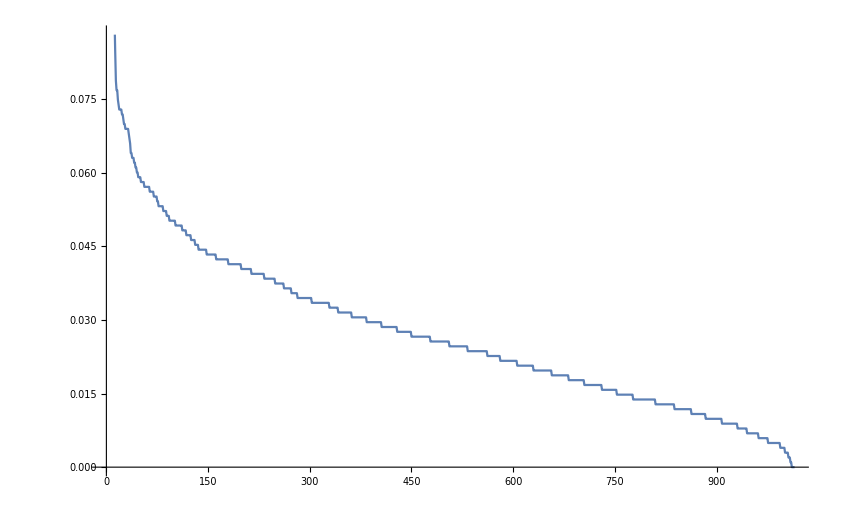

```mathematica
ListLinePlot[reVertexdegree5]
```

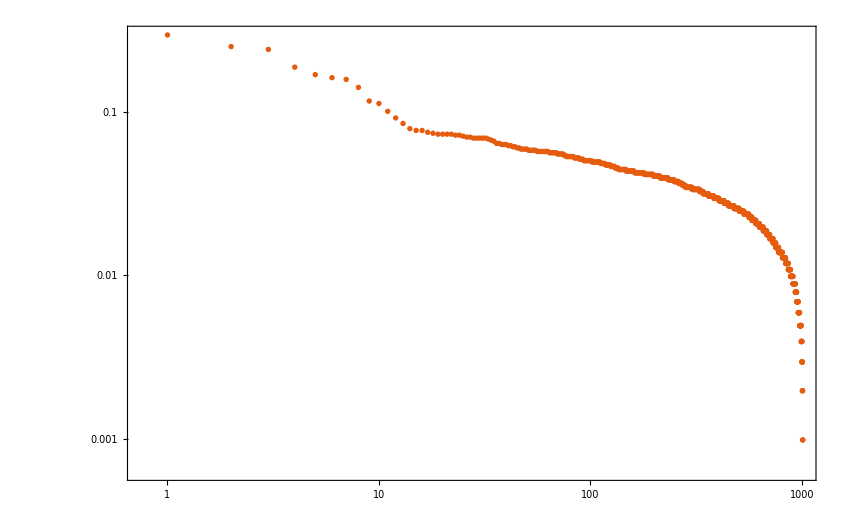

```mathematica
ListLogLogPlot[reVertexdegree5,PlotTheme->"Scientific"]
```

### - Klaszterezettségi együttható megadja, hogy a hálózat valamely pontjának a szomszédai milyen sűrűn kapcsolódnak egymáshoz.

```mathematica
meanClusteringCoefficient5 = N[MeanClusteringCoefficient[AdjacencyGraph[graph51]]];
```

```mathematica
meanClusteringCoefficient5
```

0.428765

### Átlagos távolság a hálózat csúcsai között

```mathematica
MeanGraphDistance[AdjacencyGraph[graph11]]
```

6081/3403

```mathematica
N[6081/3403]
```

1.78695